Note:
1.  J-W operators smooths out with higher site number, while the non-local sp operators do not.
2.  as location number increases, plateau of J-W ops increases, except 7.
3.  as number of sites with the σ^+ op increases, plateau maximizes at 4-site. 
	Questions: does this hold for increase in non-locality with other operators? for a random mix of Hermitian operators? (presumably yes)
4. There is no Z2 end-to-end flip symmetry for the complexity of J-W operators. Should we expect this?

Meeting notes:
1. generalize σ^+ to sx + i sy with θ parameter. Probably only need 0 to π/2
2. Periodic BCs

# Recursive Komplexity Analysis

## Importing Probability Amplitudes

### L=7

```mathematica
ACL7cd1=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode1.m"][[4]];
```

```mathematica
ACL7cd2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode2.m"][[4]];
```

```mathematica
ACL7cd3=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode3.m.gz"][[4]];
```

```mathematica
ACL7cd4=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode4.m.gz"][[4]];
```

```mathematica
ACL7cd5=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode5.m.gz"][[4]];
```

```mathematica
ACL7cd6=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode6.m.gz"][[4]];
```

```mathematica
ACL7cd7=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_cdMode7.m.gz"][[4]];
```

```mathematica
ACL7sp12=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_2site_sp12.m.gz"][[4]];
```

```mathematica
ACL7sp123=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_3site_sp123.m.gz"][[4]];
```

```mathematica
ACL7sp1234=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_4site_sp1234.m.gz"][[4]];
```

```mathematica
ACL7sp12345=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_5site_sp12345.m.gz"][[4]];
```

```mathematica
ACL7sp123456=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_6site_sp123456.m.gz"][[4]];
```

```mathematica
ACL7sp1234567=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_7site_sp1234567.m.gz"][[4]];
```

```mathematica
ACL7sx1=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_sxMode1.m.gz"][[4]];
```

```mathematica
ACL7sx2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_sxMode2.m.gz"][[4]];
```

```mathematica
ACL7sx3=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_sxMode3.m.gz"][[4]];
```

```mathematica
ACL7sx4=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L7_sxMode4.m.gz"][[4]];
```

### L=6 periodic

```mathematica
ACL6Pcd1=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L6_periodic_cdMode1.m.gz"][[4]];
```

```mathematica
ACL6Pcd2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L6_periodic_cdMode2.m.gz"][[4]];
```

```mathematica
ACL6Pcd3=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L6_periodic_cdMode3.m.gz"][[4]];
```

```mathematica
ACL6Pcd4=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L6_periodic_cdMode4.m.gz"][[4]];
```

```mathematica
ACL6Pcd5=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L6_periodic_cdMode5.m.gz"][[4]];
```

```mathematica
ACL6Pcd6=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L6_periodic_cdMode6.m.gz"][[4]];
```

```mathematica
ACL6Psp2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L6_periodic_spMode2.m.gz"][[4]];
```

### L=5 periodic

```mathematica
ACL5Psp2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5_periodic_spMode2.m.gz"][[4]];
```

```mathematica
ACL5Pcd2=Import["C:\\Users\\daisy\\OneDrive - University of Cape Town\\0. Masters Project\\Amplitude Coefficient calculations\\ProbAmp_L5_periodic_cdMode2.m.gz"][[4]];
```

## Extracting Komplexity from the Probability Amplitudes

```mathematica
tMax=50;
tPts=500;
Prec=200;
tVals = Table[N[tMax*(i)/(tPts),Prec], {i, 1, tPts}];
```

### c^+ operators

```mathematica
Length[ACL7cd1]
```

73

```mathematica
cutcd1=Length[ACL7cd1];
PL7cd1=Table[{tVals[[j]],Total[Abs[ACL7cd1[[1;;cutcd1,j]]]^2]},{j,1,tPts}];
KL7cd1=Table[{tVals[[j]],Range[cutcd1].Abs[ACL7cd1[[1;;cutcd1,j]]]^2},{j,1,tPts}];
```

```mathematica
cutcd2=Length[ACL7cd2]
PL7cd2=Table[{tVals[[j]],Total[Abs[ACL7cd2[[1;;cutcd2,j]]]^2]},{j,1,tPts}];
KL7cd2=Table[{tVals[[j]],Range[cutcd2].Abs[ACL7cd2[[1;;cutcd2,j]]]^2},{j,1,tPts}];
```

191

```mathematica
cutcd3=334
PL7cd3=Table[{tVals[[j]],Total[Abs[ACL7cd3[[1;;cutcd3,j]]]^2]},{j,1,tPts}];
KL7cd3=Table[{tVals[[j]],Range[cutcd3].Abs[ACL7cd3[[1;;cutcd3,j]]]^2},{j,1,tPts}];
```

334

```mathematica
cutcd4=372
PL7cd4=Table[{tVals[[j]],Total[Abs[ACL7cd4[[1;;cutcd4,j]]]^2]},{j,1,tPts}];
KL7cd4=Table[{tVals[[j]],Range[cutcd4].Abs[ACL7cd4[[1;;cutcd4,j]]]^2},{j,1,tPts}];
```

372

```mathematica
cutcd5=384
PL7cd5=Table[{tVals[[j]],Total[Abs[ACL7cd5[[1;;cutcd5,j]]]^2]},{j,1,tPts}];
KL7cd5=Table[{tVals[[j]],Range[cutcd5].Abs[ACL7cd5[[1;;cutcd5,j]]]^2},{j,1,tPts}];
```

384

```mathematica
cutcd6=388
PL7cd6=Table[{tVals[[j]],Total[Abs[ACL7cd6[[1;;cutcd6,j]]]^2]},{j,1,tPts}];
KL7cd6=Table[{tVals[[j]],Range[cutcd6].Abs[ACL7cd6[[1;;cutcd6,j]]]^2},{j,1,tPts}];
```

388

```mathematica
cutcd7=387
PL7cd7=Table[{tVals[[j]],Total[Abs[ACL7cd7[[1;;cutcd7,j]]]^2]},{j,1,tPts}];
KL7cd7=Table[{tVals[[j]],Range[cutcd7].Abs[ACL7cd7[[1;;cutcd7,j]]]^2},{j,1,tPts}];
```

387

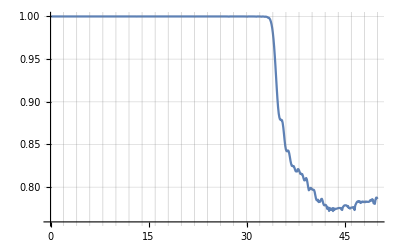

```mathematica
ListLinePlot[PL7cd7, GridLines->{Range[0,50,2], Automatic}]
```

```mathematica
Total[Abs[ACL7cd7[[1;;cutcd7,335]]]^2]
```

1.

### σ^+ operators

```mathematica
cutsp12=333
PL7sp12=Table[{tVals[[j]],Total[Abs[ACL7sp12[[1;;cutsp12,j]]]^2]},{j,1,tPts}];
KL7sp12=Table[{tVals[[j]],Range[cutsp12].Abs[ACL7sp12[[1;;cutsp12,j]]]^2},{j,1,tPts}];
```

333

```mathematica
cutsp123=385
PL7sp123=Table[{tVals[[j]],Total[Abs[ACL7sp123[[1;;cutsp123,j]]]^2]},{j,1,tPts}];
KL7sp123=Table[{tVals[[j]],Range[cutsp123].Abs[ACL7sp123[[1;;cutsp123,j]]]^2},{j,1,tPts}];
```

385

```mathematica
cutsp1234=390
PL7sp1234=Table[{tVals[[j]],Total[Abs[ACL7sp1234[[1;;cutsp1234,j]]]^2]},{j,1,tPts}];
KL7sp1234=Table[{tVals[[j]],Range[cutsp1234].Abs[ACL7sp1234[[1;;cutsp1234,j]]]^2},{j,1,tPts}];
```

390

```mathematica
cutsp12345=390
PL7sp12345=Table[{tVals[[j]],Total[Abs[ACL7sp12345[[1;;cutsp12345,j]]]^2]},{j,1,tPts}];
KL7sp12345=Table[{tVals[[j]],Range[cutsp12345].Abs[ACL7sp12345[[1;;cutsp12345,j]]]^2},{j,1,tPts}];
```

390

```mathematica
cutsp123456=384
PL7sp123456=Table[{tVals[[j]],Total[Abs[ACL7sp123456[[1;;cutsp123456,j]]]^2]},{j,1,tPts}];
KL7sp123456=Table[{tVals[[j]],Range[cutsp123456].Abs[ACL7sp123456[[1;;cutsp123456,j]]]^2},{j,1,tPts}];
```

384

```mathematica
cutsp1234567=368
PL7sp1234567=Table[{tVals[[j]],Total[Abs[ACL7sp1234567[[1;;cutsp1234567,j]]]^2]},{j,1,tPts}];
KL7sp1234567=Table[{tVals[[j]],Range[cutsp1234567].Abs[ACL7sp1234567[[1;;cutsp1234567,j]]]^2},{j,1,tPts}];
```

368

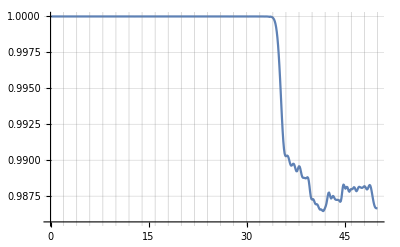

```mathematica
ListLinePlot[PL7sp1234567, PlotRange->All,  GridLines->{Range[0,50,2], Automatic}]
```

### σ^x, σ^y, σ^z operators

```mathematica
Length[ACL7sx4]
```

43

```mathematica
cutsx1=Length[ACL7sx1];
PL7sx1=Table[{tVals[[j]],Total[Abs[ACL7sx1[[1;;cutsx1,j]]]^2]},{j,1,tPts}];
KL7sx1=Table[{tVals[[j]],Range[cutsx1].Abs[ACL7sx1[[1;;cutsx1,j]]]^2},{j,1,tPts}];
```

```mathematica
cutsx2=Length[ACL7sx2];
PL7sx2=Table[{tVals[[j]],Total[Abs[ACL7sx2[[1;;cutsx2,j]]]^2]},{j,1,tPts}];
KL7sx2=Table[{tVals[[j]],Range[cutsx2].Abs[ACL7sx2[[1;;cutsx2,j]]]^2},{j,1,tPts}];
```

```mathematica
cutsx3=Length[ACL7sx3];
PL7sx3=Table[{tVals[[j]],Total[Abs[ACL7sx3[[1;;cutsx3,j]]]^2]},{j,1,tPts}];
KL7sx3=Table[{tVals[[j]],Range[cutsx3].Abs[ACL7sx3[[1;;cutsx3,j]]]^2},{j,1,tPts}];
```

```mathematica
cutsx4=Length[ACL7sx4];
PL7sx4=Table[{tVals[[j]],Total[Abs[ACL7sx4[[1;;cutsx4,j]]]^2]},{j,1,tPts}];
KL7sx4=Table[{tVals[[j]],Range[cutsx4].Abs[ACL7sx4[[1;;cutsx4,j]]]^2},{j,1,tPts}];
```

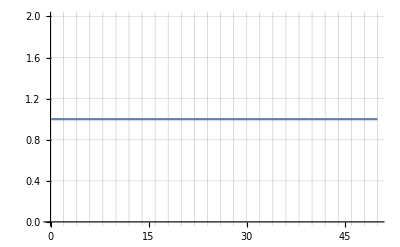

```mathematica
ListLinePlot[PL7sx4,PlotRange->All,GridLines->{Range[0,50,2],Automatic}]
```

### c^+ operators with PBCs

```mathematica
cutL6Pcd1=Length[ACL6Pcd1];
PL6Pcd1=Table[{tVals[[j]],Total[Abs[ACL6Pcd1[[1;;cutL6Pcd1,j]]]^2]},{j,1,tPts}];
KL6Pcd1=Table[{tVals[[j]],Range[cutL6Pcd1].Abs[ACL6Pcd1[[1;;cutL6Pcd1,j]]]^2},{j,1,tPts}];
```

```mathematica
cutL6Pcd2=Length[ACL6Pcd2];
PL6Pcd2=Table[{tVals[[j]],Total[Abs[ACL6Pcd2[[1;;cutL6Pcd2,j]]]^2]},{j,1,tPts}];
KL6Pcd2=Table[{tVals[[j]],Range[cutL6Pcd2].Abs[ACL6Pcd2[[1;;cutL6Pcd2,j]]]^2},{j,1,tPts}];
```

```mathematica
cutPcd3=Length[ACL6Pcd3];
PL6Pcd3=Table[{tVals[[j]],Total[Abs[ACL6Pcd3[[1;;cutPcd3,j]]]^2]},{j,1,tPts}];
KL6Pcd3=Table[{tVals[[j]],Range[cutPcd3].Abs[ACL6Pcd3[[1;;cutPcd3,j]]]^2},{j,1,tPts}];
```

```mathematica
cutPcd4=Length[ACL6Pcd4];
PL6Pcd4=Table[{tVals[[j]],Total[Abs[ACL6Pcd4[[1;;cutPcd4,j]]]^2]},{j,1,tPts}];
KL6Pcd4=Table[{tVals[[j]],Range[cutPcd4].Abs[ACL6Pcd4[[1;;cutPcd4,j]]]^2},{j,1,tPts}];
```

```mathematica
cutPcd5=Length[ACL6Pcd5];
PL6Pcd5=Table[{tVals[[j]],Total[Abs[ACL6Pcd5[[1;;cutPcd5,j]]]^2]},{j,1,tPts}];
KL6Pcd5=Table[{tVals[[j]],Range[cutPcd5].Abs[ACL6Pcd5[[1;;cutPcd5,j]]]^2},{j,1,tPts}];
```

```mathematica
cutPcd6=Length[ACL6Pcd6];
PL6Pcd6=Table[{tVals[[j]],Total[Abs[ACL6Pcd6[[1;;cutPcd6,j]]]^2]},{j,1,tPts}];
KL6Pcd6=Table[{tVals[[j]],Range[cutPcd6].Abs[ACL6Pcd6[[1;;cutPcd6,j]]]^2},{j,1,tPts}];
```

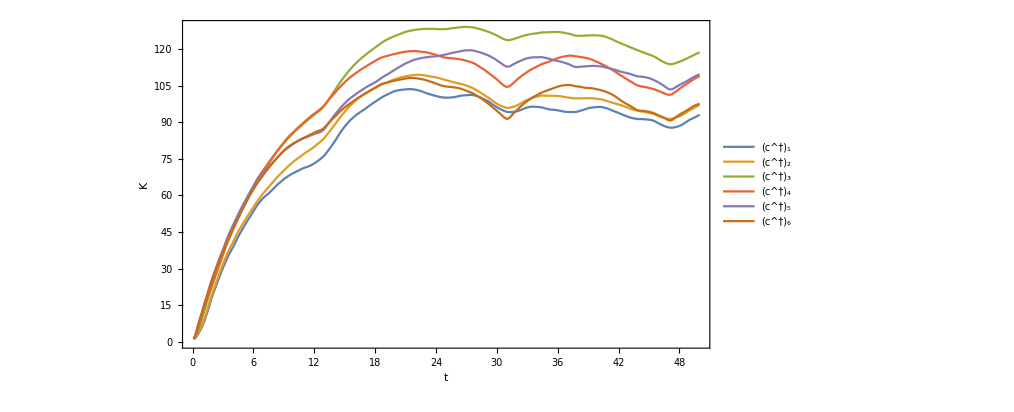

```mathematica
ListLinePlot[{KL6Pcd1,KL6Pcd2,KL6Pcd3,KL6Pcd4,KL6Pcd5,KL6Pcd6},AxesLabel->{"t","K"}, PlotRange->{{0,50},Automatic}, PlotLegends->Placed[{
Style[ ToExpression["(c^\\dagger)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(4)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(5)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(6)", TeXForm, HoldForm], Small]},{0.85,0.35}],Evaluate@Sequence@@FrameSpecsKtMulti]
```

```mathematica
cutL5Pcd2=150
PL5Pcd2=Table[{tVals[[j]],Total[Abs[ACL5Pcd2[[1;;cutL5Pcd2,j]]]^2]},{j,1,tPts}];
KL5Pcd2=Table[{tVals[[j]],Range[cutL5Pcd2].Abs[ACL5Pcd2[[1;;cutL5Pcd2,j]]]^2},{j,1,tPts}];
```

150

```mathematica
cutL5Psp2=150
PL5Psp2=Table[{tVals[[j]],Total[Abs[ACL5Psp2[[1;;cutL5Psp2,j]]]^2]},{j,1,tPts}];
KL5Psp2=Table[{tVals[[j]],Range[cutL5Psp2].Abs[ACL5Psp2[[1;;cutL5Psp2,j]]]^2},{j,1,tPts}];
```

150

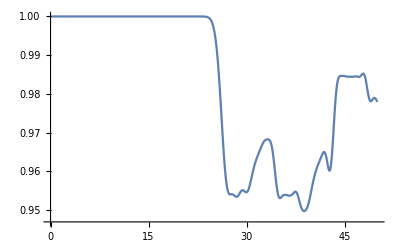

```mathematica
ListLinePlot[PL5Pcd2]
```

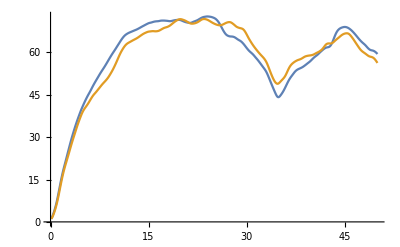

```mathematica
ListLinePlot[{KL5Pcd2,KL5Psp2}]
```

### σ^+ operators with PBC’s

```mathematica
cutPsp2=Length[ACL6Psp2];
PL6Psp2=Table[{tVals[[j]],Total[Abs[ACL6Psp2[[1;;cutPsp2,j]]]^2]},{j,1,tPts}];
KL6Psp2=Table[{tVals[[j]],Range[cutPsp2].Abs[ACL6Psp2[[1;;cutPsp2,j]]]^2},{j,1,tPts}];
```

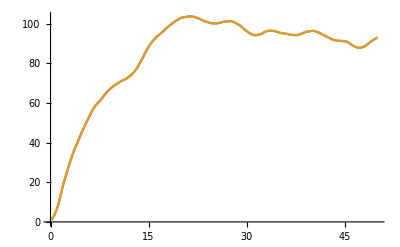

```mathematica
ListLinePlot[{KL6Pcd1,KL6Psp2}]
```

## Comparisons

### Operators compared amongst themselves

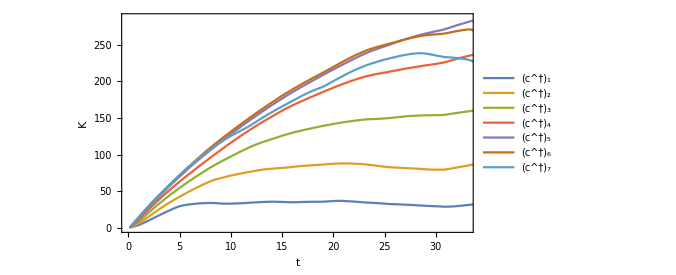

```mathematica
ListLinePlot[{KL7cd1,KL7cd2,KL7cd3,KL7cd4,KL7cd5,KL7cd6,KL7cd7},
AxesLabel->{"t","K"}, PlotRange->{{0,33},Automatic}, PlotLegends->Placed[{
Style[ ToExpression["(c^\\dagger)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(4)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(5)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(6)", TeXForm, HoldForm], Small],
Style[ ToExpression["(c^\\dagger)_(7)", TeXForm, HoldForm], Small]},{0.1,0.65}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

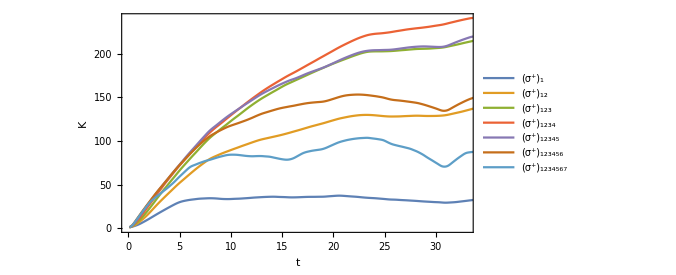

```mathematica
ListLinePlot[{KL7cd1,KL7sp12,KL7sp123,KL7sp1234,KL7sp12345,KL7sp123456,KL7sp1234567},
AxesLabel->{"t","K"}, PlotRange->{{0,33},Automatic}, PlotLegends->Placed[{
Style[ ToExpression["(\\sigma^+)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(123456)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(1234567)", TeXForm, HoldForm], Small]},{0.1,0.65}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

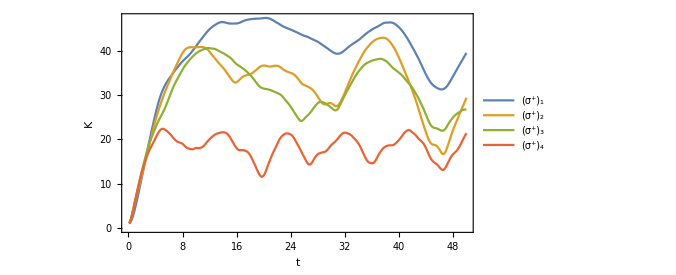

```mathematica
ListLinePlot[{KL7sx1,KL7sx2,KL7sx3,KL7sx4},
AxesLabel->{"t","K"}, PlotRange->{{0,50},Automatic}, PlotLegends->Placed[{
Style[ ToExpression["(\\sigma^+)_(1)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(2)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(3)", TeXForm, HoldForm], Small],
Style[ ToExpression["(\\sigma^+)_(4)", TeXForm, HoldForm], Small]},{0.15,0.19}],
Evaluate@Sequence@@FrameSpecsKtMulti]
```

### Multi-site σ^+ vs J-W

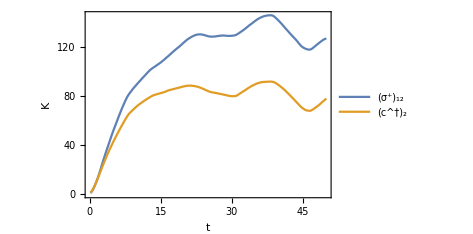

```mathematica
sp12vscd2=ListLinePlot[{KL7sp12,KL7cd2}, AxesLabel->{"t","K"}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12)", TeXForm, HoldForm], Medium],Style[ToExpression["(c^\\dagger)_2", TeXForm, HoldForm], Medium]},{0.2,0.8}],
Evaluate@Sequence@@FrameSpecsKt]
```

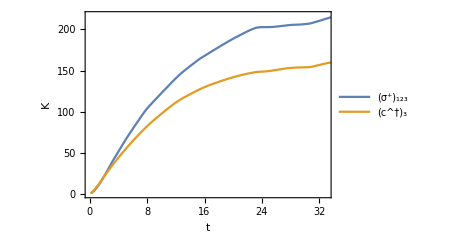

```mathematica
sp123vscd3=ListLinePlot[{KL7sp123,KL7cd3}, AxesLabel->{"t","K"}, PlotRange->{{0,33},Automatic}, PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(123)", TeXForm, HoldForm], Medium],Style[ToExpression["(c^\\dagger)_3", TeXForm, HoldForm], Medium]},{0.2,0.8}],
Evaluate@Sequence@@FrameSpecsKt]
```

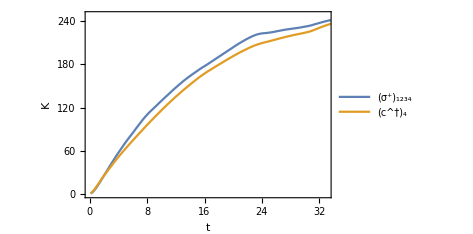

```mathematica
sp1234vscd4=ListLinePlot[{KL7sp1234,KL7cd4}, AxesLabel->{"t","K"}, PlotRange->{{0,33},Automatic},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(1234)", TeXForm, HoldForm], Medium],Style[ToExpression["(c^\\dagger)_4", TeXForm, HoldForm], Medium]},{0.2,0.8}],
Evaluate@Sequence@@FrameSpecsKt]
```

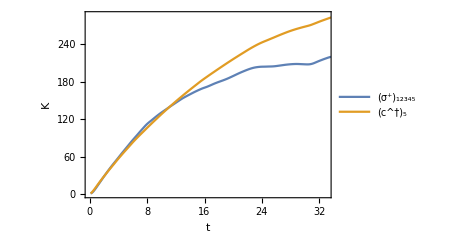

```mathematica
sp12345vscd5=ListLinePlot[{KL7sp12345,KL7cd5}, AxesLabel->{"t","K"}, PlotRange->{{0,33},Automatic},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(12345)", TeXForm, HoldForm], Medium],Style[ToExpression["(c^\\dagger)_5", TeXForm, HoldForm], Medium]},{0.2,0.8}],
Evaluate@Sequence@@FrameSpecsKt]
```

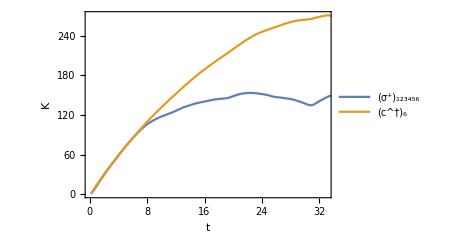

```mathematica
sp123456vscd6=ListLinePlot[{KL7sp123456,KL7cd6}, AxesLabel->{"t","K"}, PlotRange->{{0,33},Automatic},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(123456)", TeXForm, HoldForm], Medium],Style[ToExpression["(c^\\dagger)_6", TeXForm, HoldForm], Medium]},{0.2,0.8}],
Evaluate@Sequence@@FrameSpecsKt]
```

```mathematica
Text[Style[
    ToExpression["\\sigma^+", TeXForm, HoldForm], Medium], {Pi, .5}]
```

Text[σ^+,{π,0.5}]

```mathematica
Style[{Text["Frequency",Scaled@{.5,.02}],Rotate[Text["Power",Scaled@{.03,.5}],90 Degree]},14,FontFamily->"Helvetica"]
```

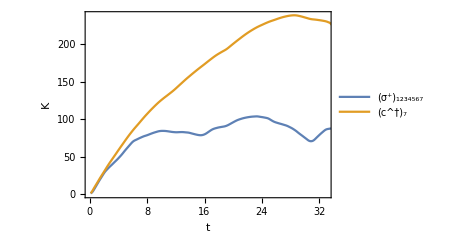

```mathematica
sp1234567vscd7=ListLinePlot[{KL7sp1234567,KL7cd7}, PlotRange->{{0,33},Automatic},
 PlotLegends->Placed[{Style[ ToExpression["(\\sigma^+)_(1234567)", TeXForm, HoldForm], Medium],Style[ToExpression["(c^\\dagger)_7", TeXForm, HoldForm], Medium]},{0.2,0.8}],
Evaluate@Sequence@@FrameSpecsKt]
```

## Plotting the stuff nicely

#### Multi-site σ^+ vs J-W

```mathematica
FrameSpecsKt={Frame->{{True,True},{True,True}},FrameLabel->{{"K",None},{"t",None}},FrameTicks->{{True,True},{True,True}},ImageSize->350,AspectRatio->0.67};
```

```mathematica
FrameSpecsKtMulti={Frame->{{True,True},{True,True}},FrameLabel->{{"K",None},{"t",None}},FrameTicks->{{True,True},{True,True}},ImageSize->500,AspectRatio->0.55};
```

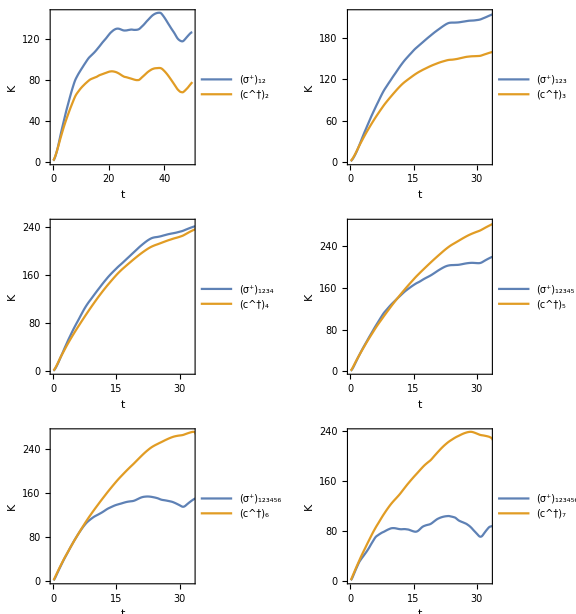

```mathematica
GraphicsGrid[{{sp12vscd2,sp123vscd3},{sp1234vscd4,sp12345vscd5},{sp123456vscd6,sp1234567vscd7}},ImageSize->Large]
```